```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

#### Range of densities

```mathematica
{triggermass[0.85],triggermass[1.37]}
```

{0.00337513,0.0000124363}

```mathematica
{Massreverse[0.85],Massreverse[1.25],Massreverse[1.37]}
```

{7.1606,8.46005,9.50943}

```mathematica
{Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->7.16},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->8.46},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->9.5}}
```

{(7.20147×10^29)/Centimeter^3,(1.43688×10^31)/Centimeter^3,(1.57551×10^32)/Centimeter^3}

```mathematica
6*{(7.201468136264897*^29)/Centimeter^3,(1.4368817984738546*^31)/Centimeter^3,(1.5755095624615844*^32)/Centimeter^3}
```

{(4.32088×10^30)/Centimeter^3,(8.62129×10^31)/Centimeter^3,(9.45306×10^32)/Centimeter^3}

```mathematica
Convert[9.453057374769507*^32 Centimeter^-3(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

7.56245 ElectronVolt^3 Mega^3

WD data

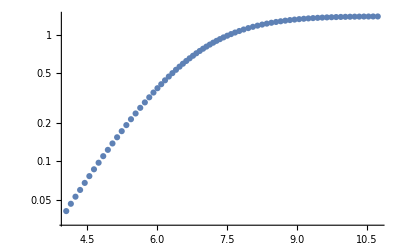

```mathematica
ListLogPlot[WD]
```

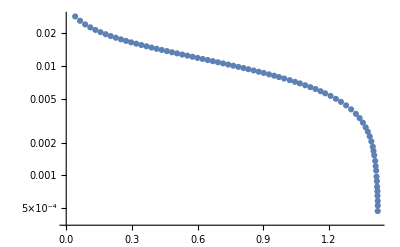

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Convert[Radplot[1.25]SolarRadius,Kilo Meter]
```

3328.47 Kilo Meter

```mathematica
Convert[Radplot[0.85]SolarRadius,Kilo Meter]
```

6392.93 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.0235528

```mathematica
vesc[0.85]
```

0.0140142

```mathematica
Radplot[1.40]
```

0.00185935

```mathematica
vesc[1.42]
```

0.0610014

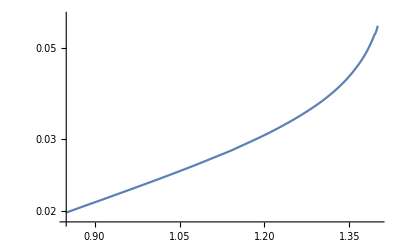

```mathematica
LogPlot[vesc[M],{M,0.85,1.4}]
```

#### trigger size, E_boom (GeV)

```mathematica
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.6,0.01}]];
10^logρ Convert[Gram/Centimeter^3 1/(12 Giga ElectronVolt/SpeedOfLight^2)*(200 Mega ElectronVolt Fermi)^3,(Mega ElectronVolt)^3]*(1/(Mega ElectronVolt))^3;
nionMeV[M_]:=Convert[10^Massreverse[M] Gram/Centimeter^3*SpeedOfLight^2/(12Giga ElectronVolt)*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]*1/(Mega ElectronVolt)^3
nionMeV2[logρ_]:=3.7397260789901873*^-10 10^logρ
eboom[M_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(triggermass[M](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV[M],Z->6})]
eboomdensity[logρ_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(trigger[10^logρ](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV2[logρ],Z->6})]
eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.40,0.01}],InterpolationOrder->1][mdm]
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,None},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_⊙)","ℰ_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> {Directive[Bold],Medium},ImageSize->Large];
```

#### How much of the WD detector should we observe?

```mathematica
restrict=1/2;
```

#### SN information

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
integralcollision[logmdm_]:=Re[NIntegrate[vesc[x]^3 (4π)/3(Radplot[x]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlesscollision=Convert[snrate*((10^logmdm Giga ElectronVolt)/(0.4 (Giga ElectronVolt)/Centimeter^3))^2((10^-3 SpeedOfLight)^2)/(SpeedOfLight^3*SolarRadius^3),Centimeter^2] 1/Centimeter^2;
```

```mathematica
integraldecay[logmdm_]:=Re[NIntegrate[vesc[1.25] (4π)/3(Radplot[1.25]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlessdecay=Convert[1/snrate (0.4(Giga ElectronVolt)/Centimeter^3)/(10^logmdm Giga ElectronVolt)(SpeedOfLight SolarRadius^3)/(10^-3 SpeedOfLight),Giga Year] 1/(Giga Year);
```

#### DM Wind - Collision Constraints

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3(Rwd*restrict)^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->eboom[1.25]
```

2.87303×10^-20

```mathematica
σobsNuStar/.logmdm->eboom[1.25]
```

4.59686×10^-27

```mathematica
eboom[1.4]
```

15.0338

```mathematica
(Log10[unitlesscollision 1/integralcollision[15.04]]/.logmdm->15.04)
```

-16.6446

```mathematica
Table[{logmdm,Log10[unitlesscollision 1/integralcollision[logmdm]]},{logmdm,15.04,24,0.1}];
```

$Aborted

```mathematica
SNlist={{15.04,-16.10406176129751},{15.139999999999999,-17.172399046810057},{15.239999999999998,-17.291977329160385},{15.34,-17.292168309046474},{15.44,-17.24315844948377},{15.54,-17.204526058483797},{15.639999999999999,-17.214178641793193},{15.739999999999998,-17.191167884183987},{15.84,-17.19198571688968},{15.94,-17.18622987721764},{16.04,-17.1869120551312},{16.14,-17.199547138311367},{16.24,-17.218634919596216},{16.34,-17.250999604393925},{16.439999999999998,-17.294111333374023},{16.54,-17.347238299142795},{16.64,-17.41419384266277},{16.74,-17.482208618206958},{16.84,-17.562068159874723},{16.939999999999998,-17.65044375555382},{17.04,-17.743089164157265},{17.14,-17.839315526309125},{17.24,-17.937722097954524},{17.34,-18.038769966686523},{17.439999999999998,-17.975451222862187},{17.54,-17.849595363164497},{17.64,-17.7110444768282},{17.74,-17.572148396772256},{17.84,-17.432690310794737},{17.939999999999998,-17.293532988828026},{18.04,-17.15408243113624},{18.14,-17.015483957841823},{18.24,-16.87671637990075},{18.34,-16.738976164649046},{18.439999999999998,-16.60085088332797},{18.54,-16.46334864820152},{18.64,-16.325318605592454},{18.74,-16.18738392111567},{18.84,-16.049068491692918},{18.939999999999998,-15.91049875914166},{19.04,-15.77172048843425},{19.14,-15.632431729604466},{19.24,-15.49295363259842},{19.34,-15.35287219889305},{19.439999999999998,-15.212495521044529},{19.54,-15.07176863984791},{19.64,-14.930598726671715},{19.74,-14.78953668182063},{19.84,-14.64797553376806},{19.939999999999998,-14.50623649653608},{20.04,-14.364021599992506},{20.14,-14.22115719133776},{20.24,-14.077599905133166},{20.34,-13.93333797053565},{20.439999999999998,-13.788402876276049},{20.54,-13.643150562657862},{20.64,-13.497413050434492},{20.74,-13.351457259907141},{20.84,-13.205198832750712},{20.939999999999998,-13.058292134333728},{21.04,-12.910782296523378},{21.14,-12.762505718485759},{21.24,-12.613412245599832},{21.34,-12.463559876734976},{21.439999999999998,-12.313036262805307},{21.54,-12.16175487599537},{21.64,-12.00974471698437},{21.74,-11.857004540104834},{21.84,-11.703381486648412},{21.939999999999998,-11.54887739522484},{22.04,-11.393399255587388},{22.14,-11.2370535738019},{22.24,-11.07162583960384},{22.34,-10.871625839603837},{22.439999999999998,-10.671625839603841},{22.54,-10.471625839603838},{22.64,-10.271625839603836},{22.74,-10.07162583960384},{22.84,-9.871625839603837},{22.939999999999998,-9.671625839603841},{23.04,-9.471625839603838},{23.14,-9.271625839603836},{23.240000000000002,-9.071625839603833},{23.34,-8.871625839603837},{23.439999999999998,-8.671625839603841},{23.54,-8.471625839603838},{23.64,-8.271625839603836},{23.740000000000002,-8.071625839603833},{23.84,-7.871625839603837},{23.939999999999998,-7.671625839603841}};
```

```mathematica
collisionSNwhole[logmdm_]:=If[logmdm≥24,Interpolation[SNlist][23.5]+2(logmdm-23.5),Interpolation[SNlist][logmdm]]
SNcollision=Plot[collisionSNwhole[logmdm],{logmdm,15.04,30},PlotStyle->{Black,Thick}];
```

```mathematica
eboomlimitcollisionf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-100,10}];
eboomlimitcollisionf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{-100,10}];
collisionlimitSN=Plot[( 100 Sign[x-eboom[1.40]]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.0065],Black}],PlotRange->{-16.104061761297505,5}];
RXcollision=Plot[Log10[σobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];
XLabelCollision={{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"},{18,"10^18"},{20,"10^20"},{22,"10^22"},{24,"10^24"},{26,"10^26"},{28,"10^28"},{30,"10^30"}};
YLabelCollision={{-80,"10^-80"},{-75,"10^-75"},{-70,"10^-70"},{-65,"10^-65"},{-60,"10^-60"},{-55,"10^-55"},{-50,"10^-50"},{-45,"10^-45"},{-40,"10^-40"},{-35,"10^-35"},{-30,"10^-30"},{-25,"10^-25"},{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"}};
canvascollisionf1=Plot[-100,{logmdm,15.1,25},Frame->True,FrameTicks->{{YLabelCollision,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_χ (GeV)", "σ_χχ (cm^2)"},LabelStyle-> {Directive[Bold],Medium},PlotRange->{-28,1},Axes->None];
```

```mathematica
SNcollisionregionplot=RegionPlot[{Log10[σHalo]>σ>collisionSNwhole[logmdm]},{logmdm,15.04,30},{σ,-20,10}];
```

InterpolatingFunction::dmval: Input value {23.9963} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9471} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9717} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

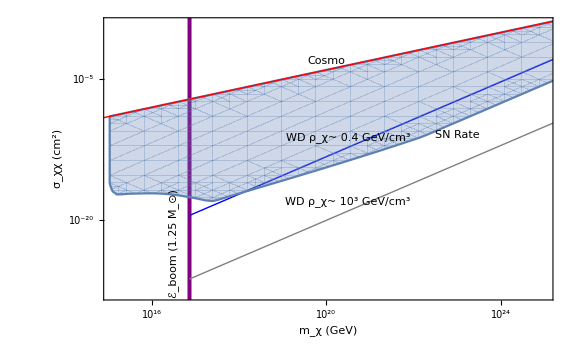

```mathematica
collisionobservation=Show[canvascollisionf1,eboomlimitcollisionf1,RXcollision, NuStarcollision,SNcollisionregionplot,σHaloplot,Graphics[Inset[Style["WD ρ_χ~ 0.4 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{20.5,-11.2},{0,0},10,{1,1/2.5}]],Graphics[Inset[Style["WD ρ_χ~ 10^3 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{20.5,-18.1},{0,0},10,{1,1/2.5}]],Graphics[Inset[Style["SN Rate",Medium,Black,FontFamily->"Helvetica"],{23,-11},{0,0},10,{1,1/2}]],Graphics[Inset[Style["ℰ_boom (1.25 M_⊙)",Medium,Black,FontFamily->"Helvetica"],{16.5,-22.5},{0,0},10,{0,1}]],Graphics[Inset[Style["Cosmo",Medium,Black,FontFamily->"Helvetica"],{20,-3},{0,0},10,{1,1/3}]],ImageSize->Large]
```

#### DM Wind - Decay Constraints

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3(Rwd restrict)^3;
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->eboom[1.25]
```

3.15562×10^11

```mathematica
τobsNuStar/.logmdm->eboom[1.25]
```

7.88906×10^14

```mathematica
Log10[unitlessdecay integraldecay[15.04]]/.logmdm->15.04
```

5.06183

```mathematica
SNlistdecay=Table[{logmdm,Log10[unitlessdecay integraldecay[logmdm]]},{logmdm,15.04,24,0.1}];
```

$Aborted

```mathematica
SNlistdecay
```

```mathematica
SNlistdecay={{15.04,5.061829204847497},{15.139999999999999,6.214449275371579},{15.239999999999998,6.420589455810837},{15.34,6.510461040359902},{15.44,6.551544112979498},{15.54,6.598983262457922},{15.639999999999999,6.6856613499137305},{15.739999999999998,6.739440702499228},{15.84,6.810654823208336},{15.94,6.87409651751223},{16.04,6.941603890234163},{16.14,7.018476255467032},{16.24,7.100924160863706},{16.34,7.195626583705712},{16.439999999999998,7.301378901121159},{16.54,7.41810524681221},{16.64,7.54973122020263},{16.74,7.685465761743471},{16.84,7.834576812918031},{16.939999999999998,7.994203637136746},{17.04,8.160348433582529},{17.14,8.33212650625868},{17.24,8.508515604189945},{17.34,8.68944064906932},{17.439999999999998,8.717377216011768},{17.54,8.68690718694907},{17.64,8.644664523237047},{17.74,8.602230683947052},{17.84,8.559395960846766},{17.939999999999998,8.51696563349105},{18.04,8.474353931738168},{18.14,8.43261081928965},{18.24,8.390759744502407},{18.34,8.349933933008959},{18.439999999999998,8.308791626797166},{18.54,8.26830106438931},{18.64,8.227370599695131},{18.74,8.186595386189007},{18.84,8.145522491925444},{18.939999999999998,8.104275333651207},{19.04,8.06289985152446},{19.14,8.02110489008738},{19.24,7.979195254970561},{19.34,7.9367661371903155},{19.439999999999998,7.894108112253941},{19.54,7.851166934406992},{19.64,7.8078527462422915},{19.74,7.764699029448229},{19.84,7.721122618226387},{19.939999999999998,7.677434099756068},{20.04,7.633345861905258},{20.14,7.5886904443392265},{20.24,7.543425648510447},{20.34,7.497537414166098},{20.439999999999998,7.451052903816492},{20.54,7.404311306028331},{20.64,7.357146431243585},{20.74,7.309819417282067},{20.84,7.262253460809001},{20.939999999999998,7.214119075568504},{21.04,7.165459681707677},{21.14,7.116111599627434},{21.24,7.066012862544948},{21.34,7.015215771441305},{21.439999999999998,6.963808844192963},{21.54,6.911716347424954},{21.64,6.858982016750252},{21.74,6.805603420150687},{21.84,6.751421635511648},{21.939999999999998,6.6964179758545805},{22.04,6.640493313700964},{22.14,6.583753107612602},{22.24,6.518052789531721},{22.34,6.418052789531719},{22.439999999999998,6.3180527895317224},{22.54,6.218052789531721},{22.64,6.11805278953172},{22.74,6.018052789531722},{22.84,5.91805278953172},{22.939999999999998,5.8180527895317224},{23.04,5.718052789531721},{23.14,5.61805278953172},{23.240000000000002,5.518052789531718},{23.34,5.41805278953172},{23.439999999999998,5.3180527895317224},{23.54,5.218052789531721},{23.64,5.11805278953172},{23.740000000000002,5.018052789531717},{23.84,4.91805278953172},{23.939999999999998,4.8180527895317224}};
```

```mathematica
decaySNwhole[logmdm_]:=If[logmdm≥24,Interpolation[SNlistdecay][23.5]-(logmdm-23.5),Interpolation[SNlistdecay][logmdm]]
```

```mathematica
SNdecay=Plot[decaySNwhole[logmdm],{logmdm,15.04,30},PlotStyle->{Black,Thick}];
```

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];eboomlimitdecayf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{0,20}];
eboomlimitdecayf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{3.5,20}];
decaylimitSN=Plot[(100 Sign[x-eboom[1.4]]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.006],Black}],PlotRange->{-10,5.061829204847496}];
YLabelDecay={{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}};
canvasdecayf1=Plot[-100,{logmdm,15,24},Frame->True,FrameTicks->{{YLabelDecay,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_χ (GeV)", "τ_χ (Gyr)"},LabelStyle-> {Directive[Bold],Medium},PlotRange->{1.3,15},Axes->None];
```

```mathematica
SNdecayregionplot=RegionPlot[{2≤τ≤decaySNwhole[logmdm]},{logmdm,15.04,30},{τ,0,10}];
```

InterpolatingFunction::dmval: Input value {23.9963} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9471} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

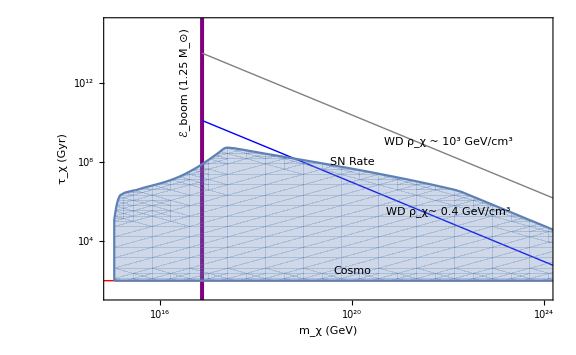

```mathematica
decayobservation=Show[canvasdecayf1,eboomlimitdecayf1,RXdecay,NuStardecay,SNdecayregionplot,τCosmoplot,Graphics[Inset[Style["WD ρ_χ~ 0.4 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{22,5.5},{0,0},10,{1,-1/2.5}]],Graphics[Inset[Style["WD ρ_χ ~ 10^3 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{22,9},{0,0},10,{1,-1/2.5}]],Graphics[Inset[Style["SN Rate",Medium,Black,FontFamily->"Helvetica"],{20,8},{0,0},10,{1,-1/10}]],Graphics[Inset[Style["ℰ_boom (1.25 M_⊙)",Medium,Black,FontFamily->"Helvetica"],{16.5,12},{0,0},10,{0,1}]],Graphics[Inset[Style["Cosmo",Medium,Black,FontFamily->"Helvetica"],{20,2.5},{0,0},10,{1,0}]],ImageSize->Large]
```

#### Transit Constraints, ϵ (in MeV!) released per collision

```mathematica
transitboom[M_]:=(((10^eboom[M] 10^3)MeV)/(nionMeV[M] MeV^3(triggermass[M]cm*(200 MeV*10^-13 cm)^-1))1/(1 ϵ MeV)(200 MeV *10^-13 cm)^2)1/cm^2;
```

```mathematica
transitreverse=Interpolation[Table[{Log10[transitboom[M]],M}/.{ϵ->10^6},{M,0.4,1.4,0.01}],InterpolationOrder->1];
integraltransit[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi (restrict Radplot[x])^2 10^10 whitedwarfdistribution[x],{x,(If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]),1.40}]]
transitfun=Convert[(ρdm/mdm)π Rwd^2(vesc/v)^2 v/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},1/Century];
unitlesstransit=Convert[1/snrate*0.4 (Giga ElectronVolt)/Centimeter^3*SpeedOfLight^2/(10^-3 SpeedOfLight)*SolarRadius^2,Giga ElectronVolt] 1/(Giga ElectronVolt);
```

```mathematica
transitRX=Log10[Convert[ρdm π (restrict Rwd)^2(vesc/v)^2 v τwd/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4(Giga ElectronVolt)/Centimeter^3,τwd->5 Giga Year},Giga ElectronVolt] 1/(Giga ElectronVolt)];
transitNuStar=Log10[Convert[ρdm π (restrict Rwd)^2(vesc/v)^2 v τwd/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3(Giga ElectronVolt)/Centimeter^3,τwd->5 Giga Year},Giga ElectronVolt] 1/(Giga ElectronVolt)];
```

```mathematica
Log10[transitboom[1.40]]/.ϵ->10^6
```

-15.7731

```mathematica
Log10[transitboom[0.85]]/.ϵ->10^6
```

-8.13791

```mathematica
SNtransitlineTeV=Log10[unitlesstransit integraltransit[Log10[transitboom[0.85]]/.ϵ->10^6]];
SNtransitlineTeVflat=Log10[unitlesstransit integraltransit[Log10[transitboom[1.3999]]/.ϵ->10^6]];
```

```mathematica
interpolateSN=Table[{Log10[unitlesstransit integraltransit[logσ]],logσ},{logσ,Log10[transitboom[1.3999]]/.ϵ->10^6,Log10[transitboom[0.85]]/.ϵ->10^6,0.01}];
```

$Aborted

```mathematica
interpolateSN
```

```mathematica
interpolateSN={{36.96826877174541,-15.76119878196517},{37.235223189518386,-15.75119878196517},{37.400442779326646,-15.74119878196517},{37.52068457085756,-15.73119878196517},{37.61543139527145,-15.721198781965171},{37.69373359604403,-15.71119878196517},{37.76054069487223,-15.70119878196517},{37.818856759457745,-15.69119878196517},{37.87064282651597,-15.68119878196517},{37.91725003989601,-15.67119878196517},{37.95964895274996,-15.66119878196517},{37.9985602652211,-15.65119878196517},{38.03453383773907,-15.641198781965171},{38.067998746061114,-15.63119878196517},{38.0992962486057,-15.62119878196517},{38.128702220938166,-15.61119878196517},{38.15644285420697,-15.60119878196517},{38.18270590767823,-15.59119878196517},{38.20764894564427,-15.58119878196517},{38.23140547937312,-15.57119878196517},{38.254089622658476,-15.561198781965171},{38.27579967277765,-15.55119878196517},{38.29662090141213,-15.54119878196517},{38.31662775587916,-15.53119878196517},{38.33588561414473,-15.52119878196517},{38.3544521979458,-15.51119878196517},{38.37237872095593,-15.50119878196517},{38.38971082945988,-15.49119878196517},{38.4064893789664,-15.48119878196517},{38.42275107994129,-15.471198781965171},{38.438529038266914,-15.46119878196517},{38.45385321037346,-15.45119878196517},{38.46875078871419,-15.44119878196517},{38.48324652999717,-15.43119878196517},{38.497363036079854,-15.42119878196517},{38.51112099548933,-15.41119878196517},{38.52453939201009,-15.40119878196517},{38.53763568558439,-15.391198781965171},{38.55042596982129,-15.38119878196517},{38.56292510965127,-15.37119878196517},{38.575146862055846,-15.36119878196517},{38.58710398230863,-15.35119878196517},{38.59880831776465,-15.34119878196517},{38.610270890908836,-15.33119878196517},{38.62150197310604,-15.32119878196517},{38.63251115027361,-15.311198781965171},{38.6433125404672,-15.30119878196517},{38.65392349945476,-15.29119878196517},{38.66435193532355,-15.28119878196517},{38.67460512563345,-15.27119878196517},{38.68468992178306,-15.26119878196517},{38.69461278164399,-15.25119878196517},{38.704379799130116,-15.24119878196517},{38.71399673104074,-15.23119878196517},{38.72346902147359,-15.221198781965171},{38.7328018240675,-15.21119878196517},{38.742000022301625,-15.20119878196517},{38.751068248051986,-15.19119878196517},{38.76001089858165,-15.18119878196517},{38.76883215212038,-15.17119878196517},{38.77753598217242,-15.16119878196517},{38.786126170674635,-15.15119878196517},{38.794606320114255,-15.141198781965171},{38.802979864703396,-15.13119878196517},{38.811250080697164,-15.12119878196517},{38.819420095932735,-15.11119878196517},{38.82749289865919,-15.10119878196517},{38.83547134572029,-15.09119878196517},{38.84335817014626,-15.08119878196517},{38.85115598820525,-15.07119878196517},{38.85886730595971,-15.061198781965171},{38.86649452536909,-15.05119878196517},{38.874039949975824,-15.04119878196517},{38.8815057902083,-15.03119878196517},{38.88889416833154,-15.02119878196517},{38.89620712307311,-15.01119878196517},{38.90344661394951,-15.00119878196517},{38.91735188286031,-14.99119878196517},{38.93239115803974,-14.98119878196517},{38.94713193715293,-14.971198781965171},{38.96158936796947,-14.96119878196517},{38.975777477399085,-14.95119878196517},{38.98970927938433,-14.94119878196517},{39.00339687011669,-14.93119878196517},{39.0168515123223,-14.92119878196517},{39.03008371008941,-14.91119878196517},{39.043103275483205,-14.90119878196517},{39.055919388006544,-14.891198781965171},{39.0685406478091,-14.88119878196517},{39.08097512402675,-14.87119878196517},{39.09323048728222,-14.86119878196517},{39.10531392596024,-14.85119878196517},{39.11723214522023,-14.84119878196517},{39.12899146636232,-14.83119878196517},{39.14059785550575,-14.82119878196517},{39.152056949638514,-14.811198781965171},{39.16337408032226,-14.80119878196517},{39.17455429530122,-14.79119878196517},{39.1856023782337,-14.78119878196517},{39.19652286673852,-14.77119878196517},{39.20732006892614,-14.76119878196517},{39.217998078564804,-14.75119878196517},{39.228560789014566,-14.74119878196517},{39.2390119060475,-14.73119878196517},{39.2493549596592,-14.721198781965171},{39.25959331496546,-14.71119878196517},{39.26973018226765,-14.70119878196517},{39.27976862636197,-14.69119878196517},{39.28971157515959,-14.68119878196517},{39.299561827678026,-14.67119878196517},{39.30932206145805,-14.66119878196517},{39.31899483945494,-14.65119878196517},{39.32858261644814,-14.64119878196517},{39.341002285299545,-14.63119878196517},{39.35383216797246,-14.62119878196517},{39.36651851435534,-14.61119878196517},{39.37906645173768,-14.60119878196517},{39.391480836118156,-14.59119878196517},{39.40376626217575,-14.58119878196517},{39.415926838271496,-14.57119878196517},{39.42796660704272,-14.561198781965171},{39.43988953430882,-14.55119878196517},{39.45169939606123,-14.54119878196517},{39.46339979046502,-14.53119878196517},{39.47499414892772,-14.52119878196517},{39.48648574632134,-14.51119878196517},{39.497877710433784,-14.50119878196517},{39.50917303071859,-14.49119878196517},{39.52037456640451,-14.48119878196517},{39.53148505402023,-14.471198781965171},{39.542507114384144,-14.46119878196517},{39.55344325910432,-14.45119878196517},{39.56429589662902,-14.44119878196517},{39.57506733788468,-14.43119878196517},{39.585759801534714,-14.42119878196517},{39.596375418889075,-14.41119878196517},{39.60691623849235,-14.40119878196517},{39.617384230415034,-14.39119878196517},{39.627781290270846,-14.38119878196517},{39.639464803278145,-14.37119878196517},{39.65233053530581,-14.36119878196517},{39.665093699262464,-14.35119878196517},{39.677757471697426,-14.34119878196517},{39.69032504358537,-14.33119878196517},{39.70279965775156,-14.32119878196517},{39.715184089397155,-14.311198781965171},{39.727480979740804,-14.30119878196517},{39.73969285605754,-14.29119878196517},{39.75182213807562,-14.28119878196517},{39.7638711439325,-14.27119878196517},{39.775842095725864,-14.26119878196517},{39.78773712469231,-14.25119878196517},{39.79955827604316,-14.24119878196517},{39.81130751348438,-14.23119878196517},{39.82298672344501,-14.221198781965171},{39.834597719036246,-14.21119878196517},{39.84614224376164,-14.20119878196517},{39.85762197499685,-14.19119878196517},{39.869038527255924,-14.18119878196517},{39.88039345525961,-14.17119878196517},{39.89285803630863,-14.16119878196517},{39.90618504498853,-14.15119878196517},{39.91943184881855,-14.14119878196517},{39.93260066462689,-14.13119878196517},{39.945693617969816,-14.12119878196517},{39.958712748021554,-14.11119878196517},{39.9716600121436,-14.10119878196517},{39.98453729015842,-14.09119878196517},{39.99734641020326,-14.08119878196517},{40.01008930596174,-14.07119878196517},{40.02276768517053,-14.061198781965171},{40.035383141439716,-14.05119878196517},{40.047937206591776,-14.04119878196517},{40.06043135369406,-14.03119878196517},{40.07286699990998,-14.02119878196517},{40.08524550918189,-14.01119878196517},{40.09756819475718,-14.00119878196517},{40.10983632156856,-13.99119878196517},{40.12335262769708,-13.98119878196517},{40.13694761576637,-13.971198781965171},{40.15047906592022,-13.96119878196517},{40.16394849223278,-13.95119878196517},{40.17735734977673,-13.94119878196517},{40.19070703751658,-13.93119878196517},{40.20399890103018,-13.92119878196517},{40.217234235070336,-13.91119878196517},{40.230414285977844,-13.90119878196517},{40.243540253956034,-13.89119878196517},{40.256613295216084,-13.88119878196517},{40.269634524001965,-13.87119878196517},{40.282605014502785,-13.86119878196517},{40.2955258026601,-13.85119878196517},{40.308397887876794,-13.84119878196517},{40.32142218779456,-13.83119878196517},{40.3358824884818,-13.82119878196517},{40.350283829265756,-13.811198781965171},{40.364627479924366,-13.80119878196517},{40.37891466542705,-13.79119878196517},{40.39314656801756,-13.78119878196517},{40.40732432917964,-13.77119878196517},{40.4214490514932,-13.76119878196517},{40.43552180038838,-13.75119878196517},{40.449543605803825,-13.74119878196517},{40.46351546375554,-13.731198781965169},{40.47743833782183,-13.721198781965171},{40.491313160549744,-13.71119878196517},{40.50514083478773,-13.70119878196517},{40.519167435013436,-13.69119878196517},{40.534284149620554,-13.68119878196517},{40.54934693146149,-13.67119878196517},{40.564356836838826,-13.66119878196517},{40.579314887147284,-13.65119878196517},{40.594222070428856,-13.64119878196517},{40.609079342844154,-13.631198781965171},{40.623887630065575,-13.62119878196517},{40.63864782859682,-13.61119878196517},{40.65336095809189,-13.60119878196517},{40.668028173083584,-13.59119878196517},{40.68265028154239,-13.58119878196517},{40.69722805237402,-13.57119878196517},{40.712344809444474,-13.561198781965171},{40.72796956466693,-13.55119878196517},{40.74354534315558,-13.54119878196517},{40.75907297723309,-13.53119878196517},{40.774553268695605,-13.52119878196517},{40.78998699020084,-13.51119878196517},{40.8053748865822,-13.50119878196517},{40.8207176760936,-13.49119878196517},{40.83601605158912,-13.481198781965169},{40.85127068164144,-13.471198781965171},{40.866482211602815,-13.46119878196517},{40.881651264611804,-13.45119878196517},{40.89778675751565,-13.44119878196517},{40.914179195794105,-13.43119878196517},{40.93052361268518,-13.42119878196517},{40.94682070136893,-13.41119878196517},{40.963071130310766,-13.40119878196517},{40.979275544371184,-13.39119878196517},{40.995434565857465,-13.381198781965171},{41.01154879552084,-13.37119878196517},{41.027618813502286,-13.36119878196517},{41.043645062182044,-13.35119878196517},{41.059627809324574,-13.34119878196517},{41.07680797379619,-13.33119878196517},{41.09398587275419,-13.32119878196517},{41.111114893817025,-13.311198781965171},{41.12819567200191,-13.30119878196517},{41.14522882514631,-13.29119878196517},{41.162214954587384,-13.28119878196517},{41.17915464580854,-13.27119878196517},{41.196048469055114,-13.26119878196517},{41.21289697992078,-13.25119878196517},{41.22970071990626,-13.24119878196517},{41.24709154635243,-13.231198781965169},{41.264456464781276,-13.221198781965171},{41.28177476207645,-13.21119878196517},{41.29904698678106,-13.20119878196517},{41.316273673903204,-13.19119878196517},{41.33345534542302,-13.18119878196517},{41.35059251077623,-13.17119878196517},{41.36768566731528,-13.16119878196517},{41.38473530074946,-13.15119878196517},{41.40184412327744,-13.14119878196517},{41.41910203269431,-13.131198781965171},{41.436316722902326,-13.12119878196517},{41.45348888989211,-13.11119878196517},{41.470618947315195,-13.10119878196517},{41.48770729316855,-13.09119878196517},{41.504754310511174,-13.08119878196517},{41.5217603681441,-13.07119878196517},{41.53872582125576,-13.061198781965171},{41.555651012034836,-13.05119878196517},{41.57370188146931,-13.04119878196517},{41.59185108645886,-13.03119878196517},{41.60995469239918,-13.02119878196517},{41.628013066959255,-13.01119878196517},{41.64602656396693,-13.00119878196517},{41.66399552405676,-12.99119878196517},{41.68192027528402,-12.981198781965169},{41.69980113370664,-12.971198781965171},{41.717767080614294,-12.96119878196517},{41.736677915905354,-12.95119878196517},{41.75554018399296,-12.94119878196517},{41.7743542118684,-12.93119878196517},{41.793120303136945,-12.92119878196517},{41.811838477662164,-12.91119878196517},{41.830508926468916,-12.90119878196517},{41.84913196467084,-12.89119878196517},{41.867707902268116,-12.881198781965171},{41.88669113295984,-12.87119878196517},{41.90570006506847,-12.86119878196517},{41.92466013551503,-12.85119878196517},{41.94357166034823,-12.84119878196517},{41.96243495055252,-12.83119878196517},{41.98125031216971,-12.82119878196517},{42.00001804641703,-12.811198781965171},{42.018738449801454,-12.80119878196517},{42.03793263924954,-12.79119878196517},{42.05718236012325,-12.78119878196517},{42.07638245881852,-12.77119878196517},{42.09553324273674,-12.76119878196517},{42.114635014510704,-12.75119878196517},{42.133688072116584,-12.74119878196517},{42.15269284385207,-12.731198781965169},{42.17169493897734,-12.721198781965171},{42.191281951890375,-12.71119878196517},{42.210818713264196,-12.70119878196517},{42.23030543991061,-12.69119878196517},{42.249742332413824,-12.68119878196517},{42.26912957607734,-12.67119878196517},{42.288467341816286,-12.66119878196517},{42.30775578699844,-12.65119878196517},{42.32734227008499,-12.64119878196517},{42.34714082901368,-12.631198781965171},{42.36688731212243,-12.62119878196517},{42.386581840230306,-12.61119878196517},{42.4062245228647,-12.60119878196517},{42.42581545894799,-12.59119878196517},{42.445354737443814,-12.58119878196517},{42.46500318839878,-12.57119878196517},{42.48496977891823,-12.561198781965171},{42.50488191782098,-12.55119878196517},{42.52473884572625,-12.54119878196517},{42.54454056968096,-12.53119878196517},{42.564287235839934,-12.52119878196517},{42.58397899934496,-12.51119878196517},{42.60374188584872,-12.50119878196517},{42.623871987274384,-12.49119878196517},{42.643944613949586,-12.481198781965169},{42.66395996659588,-12.471198781965171},{42.68391825246059,-12.46119878196517},{42.70381968473597,-12.45119878196517},{42.723664482016765,-12.44119878196517},{42.743649839855415,-12.43119878196517},{42.763944477477345,-12.42119878196517},{42.78417992971009,-12.41119878196517},{42.80435645297167,-12.40119878196517},{42.82447430721442,-12.39119878196517},{42.844533756950895,-12.381198781965171},{42.864535071721626,-12.37119878196517},{42.88484402710341,-12.36119878196517},{42.9052811443084,-12.35119878196517},{42.925657714705146,-12.34119878196517},{42.94597403429381,-12.33119878196517},{42.96623040027309,-12.32119878196517},{42.98642711076177,-12.311198781965171},{43.00664538529208,-12.30119878196517},{43.02725490834904,-12.29119878196517},{43.04780252630878,-12.28119878196517},{43.06828856300062,-12.27119878196517},{43.0887133420174,-12.26119878196517},{43.10907718651241,-12.25119878196517},{43.129381487707874,-12.24119878196517},{43.15011444386871,-12.231198781965169},{43.17089901136729,-12.221198781965171},{43.1916221308793,-12.21119878196517},{43.212283818265924,-12.20119878196517},{43.232884035170734,-12.19119878196517},{43.25342269289113,-12.18119878196517},{43.26823899461205,-12.17119878196517},{43.28004023856959,-12.16119878196517},{43.291820848285234,-12.15119878196517},{43.30358078096869,-12.14119878196517},{43.31531998967252,-12.131198781965171},{43.32703842347592,-12.12119878196517},{43.33873602766168,-12.11119878196517},{43.350412743886565,-12.10119878196517},{43.36206851034538,-12.09119878196517},{43.37370326192892,-12.08119878196517},{43.38531693037591,-12.07119878196517},{43.392775111079885,-12.061198781965171},{43.400170946633324,-12.05119878196517},{43.40755794496453,-12.04119878196517},{43.414935753708434,-12.03119878196517},{43.42230435668459,-12.02119878196517},{43.42966374795373,-12.01119878196517},{43.4370139228764,-12.00119878196517},{43.44435487807983,-11.99119878196517},{43.451686611425565,-11.981198781965169},{43.45900912197788,-11.971198781965171},{43.46632240997296,-11.96119878196517},{43.47362647678871,-11.95119878196517},{43.48092132491543,-11.94119878196517},{43.488206957927055,-11.93119878196517},{43.49548338045314,-11.92119878196517},{43.5027505981515,-11.91119878196517},{43.510023048775466,-11.90119878196517},{43.51732316796243,-11.89119878196517},{43.52461397475833,-11.881198781965171},{43.53189547888834,-11.87119878196517},{43.539167691003875,-11.86119878196517},{43.54643062265813,-11.85119878196517},{43.553684286282035,-11.84119878196517},{43.56092869516096,-11.83119878196517},{43.56816386341183,-11.82119878196517},{43.57538980596091,-11.811198781965171},{43.582606538521986,-11.80119878196517},{43.589814077575184,-11.79119878196517},{43.59701244034625,-11.78119878196517},{43.60420164478627,-11.77119878196517},{43.611381709551964,-11.76119878196517},{43.61855265398634,-11.75119878196517},{43.62571449809991,-11.74119878196517},{43.63297522287101,-11.731198781965169},{43.6402745797139,-11.721198781965171},{43.64756450225556,-11.71119878196517},{43.65484501453209,-11.70119878196517},{43.662116141210596,-11.69119878196517},{43.66937790757097,-11.68119878196517},{43.67663033948818,-11.67119878196517},{43.68387346341492,-11.66119878196517},{43.69110742465162,-11.65119878196517},{43.698332479222046,-11.64119878196517},{43.705548651977196,-11.631198781965171},{43.712755960724145,-11.62119878196517},{43.71995442253244,-11.61119878196517},{43.72714405375134,-11.60119878196517},{43.734324870026775,-11.59119878196517},{43.74149688631778,-11.58119878196517},{43.74876619561001,-11.571198781965169},{43.75615206021139,-11.561198781965171},{43.76352858989283,-11.55119878196517},{43.770895798222064,-11.541198781965171},{43.77825369807566,-11.53119878196517},{43.78560230165583,-11.52119878196517},{43.792941620506994,-11.51119878196517},{43.8002716655319,-11.50119878196517},{43.80759244700736,-11.49119878196517},{43.81490397459965,-11.481198781965169},{43.82220625737959,-11.471198781965171},{43.82949930383724,-11.46119878196517},{43.836783121896254,-11.45119878196517},{43.84405771892798,-11.44119878196517},{43.85132310176514,-11.43119878196517},{43.85857927671529,-11.42119878196517},{43.86600042306063,-11.411198781965169},{43.87347551457417,-11.40119878196517},{43.880940800703556,-11.39119878196517},{43.88839628618753,-11.381198781965171},{43.895841975239726,-11.37119878196517},{43.903277871562445,-11.36119878196517},{43.910703978360026,-11.35119878196517},{43.91812029835198,-11.34119878196517},{43.92552683378574,-11.33119878196517},{43.932923586449185,-11.321198781965169},{43.94031055768285,-11.311198781965171},{43.94768774839181,-11.30119878196517},{43.955055155789516,-11.291198781965171},{43.96241271117081,-11.28119878196517},{43.96976038838665,-11.27119878196517},{43.97717926332863,-11.26119878196517},{43.98466676271587,-11.25119878196517},{43.992143954515335,-11.24119878196517},{43.99961084080093,-11.231198781965169},{44.007067423658064,-11.221198781965171},{44.01451370518343,-11.21119878196517},{44.02194968748478,-11.20119878196517},{44.0293753726807,-11.19119878196517},{44.036790762900395,-11.18119878196517},{44.04419586028353,-11.17119878196517},{44.05159066697994,-11.161198781965169},{44.05897518514952,-11.15119878196517},{44.06634941696197,-11.14119878196517},{44.07371336459666,-11.131198781965171},{44.081067030242394,-11.12119878196517},{44.08848472593315,-11.11119878196517},{44.09594004196354,-11.10119878196517},{44.103384736802205,-11.09119878196517},{44.11081881278772,-11.08119878196517},{44.118242272267864,-11.071198781965169},{44.12565511759946,-11.061198781965171},{44.13305735114821,-11.05119878196517},{44.140448975288564,-11.041198781965171},{44.147829992403516,-11.03119878196517},{44.155200404884496,-11.02119878196517},{44.16256021513122,-11.01119878196517},{44.16990942555153,-11.00119878196517},{44.17724803856126,-10.99119878196517},{44.18457605658413,-10.981198781965169},{44.191893482051576,-10.971198781965171},{44.19929865820546,-10.96119878196517},{44.20669802306479,-10.95119878196517},{44.2140865008149,-10.94119878196517},{44.22146409400159,-10.93119878196517},{44.2288307818395,-10.92119878196517},{44.236186547203765,-10.911198781965169},{44.2435313942442,-10.90119878196517},{44.25086532731433,-10.89119878196517},{44.258188350965796,-10.881198781965171},{44.265500469943,-10.87119878196517},{44.27280168917779,-10.86119878196517},{44.28009201378433,-10.85119878196517},{44.287371449054085,-10.84119878196517},{44.2946400004509,-10.83119878196517},{44.30194795124696,-10.821198781965169},{44.309295096279804,-10.811198781965171},{44.31663107146922,-10.80119878196517},{44.32395588318382,-10.791198781965171},{44.331269537950156,-10.78119878196517},{44.338572042448085,-10.77119878196517},{44.345863403506435,-10.76119878196517},{44.35314362809864,-10.75119878196517},{44.36041272333855,-10.74119878196517},{44.3676706964763,-10.731198781965169},{44.37491755489432,-10.721198781965171},{44.382153306103426,-10.71119878196517},{44.38937795773898,-10.70119878196517},{44.3965915175572,-10.69119878196517},{44.403812464956104,-10.68119878196517},{44.411078645430344,-10.67119878196517},{44.41833352650537,-10.661198781965169},{44.42557711664617,-10.65119878196517},{44.43280942442556,-10.64119878196517},{44.44003045852084,-10.631198781965171},{44.44724022771046,-10.62119878196517},{44.454438745233574,-10.61119878196517},{44.46162606469649,-10.60119878196517},{44.468802205772164,-10.59119878196517},{44.47596717597514,-10.58119878196517},{44.48312098259889,-10.571198781965169},{44.490263632721295,-10.561198781965171},{44.49739513321005,-10.55119878196517},{44.50452621823493,-10.541198781965171},{44.51171192198249,-10.53119878196517},{44.51888625454994,-10.52119878196517},{44.52604922221067,-10.51119878196517},{44.53320083104498,-10.50119878196517},{44.54034108694504,-10.49119878196517},{44.547469995619714,-10.481198781965169},{44.55458756259927,-10.471198781965171},{44.56169379323998,-10.46119878196517},{44.56878869272865,-10.45119878196517},{44.575872266086996,-10.44119878196517},{44.58294451817592,-10.43119878196517},{44.59000545369977,-10.42119878196517},{44.59705507721036,-10.411198781965169},{44.604111173511676,-10.40119878196517},{44.61123474847457,-10.39119878196517},{44.61834671124776,-10.381198781965171},{44.625447065975656,-10.37119878196517},{44.63253581666197,-10.36119878196517},{44.639612967173505,-10.35119878196517},{44.64667852124395,-10.34119878196517},{44.65373248247746,-10.33119878196517},{44.66077485435229,-10.321198781965169},{44.667805640224216,-10.311198781965171},{44.67482484332998,-10.30119878196517},{44.681832466790596,-10.291198781965171},{44.68882851361178,-10.28119878196517},{44.695812971725104,-10.27119878196517},{44.70283793436613,-10.26119878196517},{44.70992386648982,-10.25119878196517},{44.71699778628514,-10.24119878196517},{44.72405969741873,-10.231198781965169},{44.73110960359103,-10.221198781965171},{44.73814750853561,-10.21119878196517},{44.74517341601836,-10.20119878196517},{44.75218732983687,-10.19119878196517},{44.7591892538197,-10.18119878196517},{44.766179191825685,-10.17119878196517},{44.773157147743355,-10.161198781965169},{44.78012312549023,-10.15119878196517},{44.787077129012246,-10.14119878196517},{44.79401916228312,-10.131198781965171},{44.80104539249251,-10.12119878196517},{44.808070865456834,-10.11119878196517},{44.81508400539276,-10.10119878196517},{44.822084816573835,-10.09119878196517},{44.82907330330014,-10.08119878196517},{44.83604946989784,-10.071198781965169},{44.8430133207185,-10.061198781965171},{44.8499648601387,-10.05119878196517},{44.856904092559425,-10.041198781965171},{44.86383102240562,-10.03119878196517},{44.87074565412566,-10.02119878196517},{44.87764799219093,-10.01119878196517},{44.88453804109532,-10.00119878196517},{44.89145831022432,-9.99119878196517},{44.898397427185515,-9.981198781965169},{44.90532400343459,-9.971198781965171},{44.912238043700896,-9.96119878196517},{44.919139552735054,-9.95119878196517},{44.92602853530858,-9.94119878196517},{44.93290499097242,-9.93119878196517},{44.939768906187716,-9.92119878196517},{44.94662028495142,-9.911198781965169},{44.953459133080315,-9.90119878196517},{44.96028545653318,-9.89119878196517},{44.96709926140705,-9.881198781965171},{44.97390055393355,-9.87119878196517},{44.980698673572526,-9.86119878196517},{44.987498225169475,-9.85119878196517},{44.994285197845755,-9.84119878196517},{45.00105959840688,-9.83119878196517},{45.00782143377749,-9.821198781965169},{45.0145707109981,-9.811198781965171},{45.021307437222006,-9.80119878196517},{45.02803161971216,-9.791198781965171},{45.0347432658382,-9.78119878196517},{45.04144238307353,-9.77119878196517},{45.048128978992445,-9.76119878196517},{45.05480306126734,-9.75119878196517},{45.061464637666035,-9.74119878196517},{45.068126078090856,-9.731198781965169},{45.07480837499333,-9.721198781965171},{45.081478017159625,-9.71119878196517},{45.088135012883505,-9.70119878196517},{45.09477937054374,-9.69119878196517},{45.10141109860169,-9.68119878196517},{45.108030205598915,-9.67119878196517},{45.11463670015487,-9.661198781965169},{45.12123059096464,-9.65119878196517},{45.127811886796756,-9.64119878196517},{45.13438059649101,-9.631198781965171},{45.1409367468516,-9.62119878196517},{45.14748038600087,-9.61119878196517},{45.15402895955052,-9.60119878196517},{45.160623424925255,-9.59119878196517},{45.16720510846792,-9.58119878196517},{45.17377401664431,-9.571198781965169},{45.180330155638906,-9.561198781965171},{45.186873531362444,-9.55119878196517},{45.19340414945938,-9.541198781965171},{45.19992201531514,-9.53119878196517},{45.20642713406323,-9.52119878196517},{45.21291951059221,-9.51119878196517},{45.219399149552444,-9.50119878196517},{45.225866055362765,-9.49119878196517},{45.23232023221697,-9.481198781965169},{45.23880322808899,-9.471198781965171},{45.24535411274916,-9.46119878196517},{45.251891791108086,-9.45119878196517},{45.25841626670942,-9.44119878196517},{45.2649275428871,-9.43119878196517},{45.271425622771645,-9.42119878196517},{45.27791050929615,-9.411198781965169},{45.28438220520228,-9.40119878196517},{45.29084071304609,-9.39119878196517},{45.29728603520364,-9.381198781965171},{45.303718173876604,-9.37119878196517},{45.31013713109767,-9.36119878196517},{45.316542908735826,-9.35119878196517},{45.32300123681123,-9.34119878196517},{45.329475561711654,-9.33119878196517},{45.33593623328226,-9.321198781965169},{45.34238325540554,-9.311198781965171},{45.3488166323803,-9.30119878196517},{45.3552363689111,-9.291198781965171},{45.361642470097905,-9.28119878196517},{45.36803494142597,-9.27119878196517},{45.37441378875602,-9.26119878196517},{45.38077901831463,-9.25119878196517},{45.387130636684745,-9.24119878196517},{45.39346865079661,-9.231198781965169},{45.39980707305561,-9.221198781965171},{45.40617963839166,-9.21119878196517},{45.41253835490049,-9.20119878196517},{45.41888323106331,-9.19119878196517},{45.425214275677696,-9.18119878196517},{45.431531497849186,-9.17119878196517},{45.43783490698311,-9.161198781965169},{45.444124512776625,-9.15119878196517},{45.45040032521091,-9.14119878196517},{45.45666235454352,-9.131198781965171},{45.462910611301005,-9.12119878196517},{45.46914510627159,-9.11119878196517},{45.475365850498115,-9.10119878196517},{45.48159896507697,-9.09119878196517},{45.48782166391971,-9.08119878196517},{45.49403051567889,-9.071198781965169},{45.5002255325229,-9.061198781965171},{45.50640673705846,-9.05119878196517},{45.512574231783674,-9.041198781965171},{45.51872804808441,-9.03119878196517},{45.52486819523539,-9.02119878196517},{45.53099468194368,-9.01119878196517},{45.53710751636399,-9.00119878196517},{45.54320670611369,-8.99119878196517},{45.549292258287466,-8.981198781965169},{45.55538498374034,-8.971198781965171},{45.56147784491892,-8.96119878196517},{45.567556930621045,-8.95119878196517},{45.57362224607397,-8.94119878196517},{45.57967379604056,-8.93119878196517},{45.58571158483245,-8.92119878196517},{45.591735616322964,-8.911198781965169},{45.59774589395969,-8.90119878196517},{45.60374242077686,-8.89119878196517},{45.60972519940736,-8.881198781965171},{45.61569423209457,-8.87119878196517},{45.62164952070387,-8.86119878196517},{45.62760708472124,-8.85119878196517},{45.63357629744357,-8.84119878196517},{45.639531576494655,-8.83119878196517},{45.64547292234366,-8.821198781965169},{45.65140033512668,-8.811198781965171},{45.657313814657286,-8.80119878196517},{45.66321336043667,-8.791198781965171},{45.66909897166367,-8.78119878196517},{45.674970647244514,-8.77119878196517},{45.68082838580238,-8.76119878196517},{45.686672119357404,-8.75119878196517},{45.6925017531723,-8.74119878196517},{45.698330949382424,-8.731198781965169},{45.70418551363532,-8.721198781965171},{45.710025730578266,-8.71119878196517},{45.71585160626451,-8.70119878196517},{45.72166314754801,-8.69119878196517},{45.727460362062956,-8.68119878196517},{45.73324325820371,-8.67119878196517},{45.739011845105225,-8.661198781965169},{45.74476613262391,-8.65119878196517},{45.75050613131893,-8.64119878196517},{45.756231852433885,-8.631198781965171},{45.76194330787895,-8.62119878196517},{45.76764904215757,-8.61119878196517},{45.77336783539716,-8.60119878196517},{45.77907222234471,-8.59119878196517},{45.784762217687074,-8.58119878196517},{45.79043783670875,-8.571198781965169},{45.79609909527576,-8.561198781965171},{45.80174600981994,-8.55119878196517},{45.80737859732354,-8.541198781965171},{45.81299687530416,-8.53119878196517},{45.81860086180005,-8.52119878196517},{45.824190575355715,-8.51119878196517},{45.82976603500785,-8.50119878196517},{45.835334654077805,-8.49119878196517},{45.84090678197265,-8.481198781965169},{45.84646473754395,-8.471198781965171},{45.85200854517408,-8.46119878196517},{45.85753822084415,-8.45119878196517},{45.86305377980115,-8.44119878196517},{45.86855523657723,-8.43119878196517},{45.87404260500844,-8.42119878196517},{45.879515898253146,-8.411198781965169},{45.884975128810005,-8.40119878196517},{45.89042030853564,-8.39119878196517},{45.8958514486618,-8.381198781965171},{45.901268565357576,-8.37119878196517},{45.90667167123485,-8.36119878196517},{45.91206076755507,-8.35119878196517},{45.917435863216106,-8.34119878196517},{45.922796966571916,-8.33119878196517},{45.92814408544776,-8.321198781965169},{45.93347722715504,-8.311198781965171},{45.93879639850587,-8.30119878196517},{45.94410160582733,-8.291198781965171},{45.94939285497539,-8.28119878196517},{45.95467015134863,-8.27119878196517},{45.959933499901545,-8.26119878196517},{45.96519354388554,-8.25119878196517},{45.970449602785656,-8.24119878196517},{45.97569161607446,-8.231198781965169},{45.98091958709475,-8.221198781965171},{45.98613351515704,-8.21119878196517},{45.99133330837022,-8.20119878196517},{45.99651892977588,-8.19119878196517},{46.00169038528813,-8.18119878196517},{46.00684768146127,-8.17119878196517},{46.01199082547436,-8.161198781965169},{46.0171198251162,-8.15119878196517},{46.0222346887705,-8.14119878196517}};
```

```mathematica
transitSN=Interpolation[interpolateSN];
```

```mathematica
wholeSN[logmdm_]:=If[logmdm≤SNtransitlineTeVflat,Log10[transitboom[1.3999]/.ϵ->10^6],transitSN[logmdm]]
```

#### Model-dependent crust stopping calculation (R_crust~ 50 km, ρ_crust~ 10^-3 ρ_central)

```mathematica
crust=Log10[Convert[((10^logmdm Giga ElectronVolt vesc[1.25]^2)/(50Kilo Meter 10^-3 nionMeV[1.25](Mega ElectronVolt)^3(200 Mega ElectronVolt Fermi)^-3))1/(ϵ Mega ElectronVolt),Centimeter^2] 1/Centimeter^2];
```

```mathematica
crustplotTeV=Plot[crust/.ϵ->10^6,{logmdm,20,55},PlotStyle->{Dashed,Black,Thick}];
photontransitTeV=Plot[Log10[transitboom[1.25]]/.ϵ->10^6,{logmdm,24,52},PlotStyle->{Thick,Purple}];
transitSNTeV=Plot[wholeSN[logmdm],{logmdm,Log10[unitlesstransit integraltransit[Log10[transitboom[1.3999]]/.ϵ->10^6]],Log10[unitlesstransit integraltransit[Log10[transitboom[0.85]]/.ϵ->10^6]]},PlotStyle->{Black,Thick}];
fluxlimitRX=Plot[( 100 Sign[logmdm-transitRX]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.005],Blue}],PlotRange->{-20,10}];
fluxlimitNuStar=Plot[( 100 Sign[logmdm-transitNuStar]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.005],Gray}],PlotRange->{-20,10}];
fluxlimitSN=Plot[(100 Sign[logmdm-SNtransitlineTeV]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.0069],Black}],PlotRange->{Log10[transitboom[0.85]]/.ϵ->10^6,10}];
YLabelTransit={{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"},{5,"10^5"}};
XLabelTransit={{25,"10^25"},{30,"10^30"},{35,"10^35"},{40,"10^40"},{45,"10^45"},{50,"10^50"}};
canvastransit=Plot[-100,{x,27,50},Frame->True,FrameTicks->{{YLabelTransit,None},{XLabelTransit,None}},FrameStyle->Black,FrameLabel->{"m_χ (GeV)", "σ_Niϵ (cm^2)"},LabelStyle-> {Directive[Bold],Medium},PlotRange->{-18,3},Axes->None];
SNtransitregionplot=RegionPlot[{σ>wholeSN[logmdm]},{logmdm,24,Log10[unitlesstransit integraltransit[Log10[transitboom[0.86]]/.ϵ->10^6]]},{σ,-20,10}];
```

InterpolatingFunction::dmval: Input value {36.6674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.8259} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.8971} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.9327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

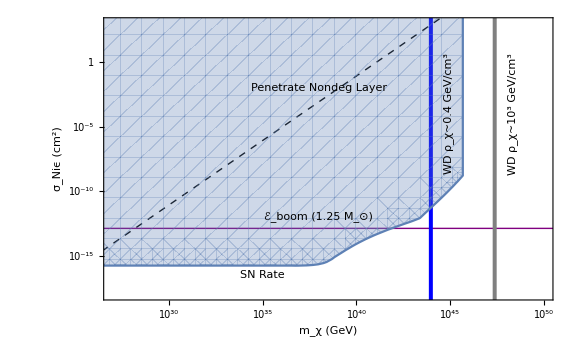

```mathematica
transitobservation=Show[canvastransit,crustplotTeV,photontransitTeV,fluxlimitRX,fluxlimitNuStar,SNtransitregionplot,Graphics[Inset[Style["ℰ_boom (1.25 M_⊙)",Medium,Black,FontFamily->"Helvetica"],{38,-12},{0,0},12,{1,0}]],
Graphics[Inset[Style["SN Rate",Medium,Black,FontFamily->"Helvetica"],{35,-16.5},{0,0},4,{1,0}]],Graphics[Inset[Style["WD ρ_χ~10^3 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{48.3,-4},{0,0},12,{0,1}]],Graphics[Inset[Style["WD ρ_χ~0.4 GeV/cm^3",Medium,Black,FontFamily->"Helvetica"],{44.9,-4},{0,0},12,{0,1}]],Graphics[Inset[Style["Penetrate Nondeg Layer",Medium,FontFamily->"Helvetica"],{38,-2},{0,0},10,{1,3/4}]],ImageSize->Large]
```

#### Competing constraints: deplete galactic halo by O(1), CMB polarization, terrestrial cosmic ray experiments, general DM decay.

```mathematica
σHalo=Convert[Barn/(ElectronVolt Giga)mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCMB=Convert[Convert[3 10^-26 Centimeter^3/Second*1/(100 Giga ElectronVolt) (((10 ElectronVolt)/(mdm Giga ElectronVolt))^(1/2)SpeedOfLight)^-1,Barn/(Giga ElectronVolt)]mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCR=Convert[1/(5Year)*(((0.3 Giga ElectronVolt)/Centimeter^3 1/(mdm Giga ElectronVolt))^2 10^-3 SpeedOfLight*(50 Kilo Meter)^2(50 Kilo Parsec))^-1,Centimeter^2] 1/Centimeter^2/.mdm->10^logmdm;
τCR=Convert[(0.3 Giga ElectronVolt)/Centimeter^3*1/(mdm Giga ElectronVolt)*(50 Kilo Meter)^2(50 Kilo Parsec)*5Year,Giga Year] 1/(Giga Year)/.mdm->10^logmdm;
τcosmo=10^2 Giga Year*1/(Giga Year);
σHaloplot=Plot[Log10[σHalo],{logmdm,-3,35},PlotStyle->{Red,Thick}];
τCosmoplot=Plot[Log10[τcosmo],{logmdm,13,35},PlotStyle->{Red,Thick}];
σCMBplot=Plot[Log10[σCMB],{logmdm,eboom[1.25],35},PlotStyle->{Green,Thick}];
σCRplot=Plot[Log10[σCR],{logmdm,eboom[1.25],35},PlotStyle->{Red,Thick}];
τCRplot=Plot[Log10[τCR],{logmdm,eboom[1.25],35},PlotStyle->{Cyan,Thick}];
```

#### Q-ball boom σ_Q

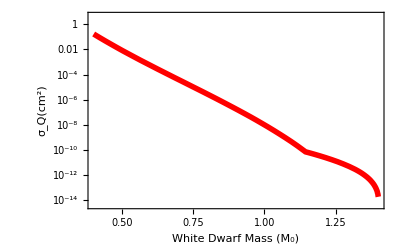

```mathematica
LogPlot[transitboom[M]/.ϵ->10^4,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

#### SUSY Q-ball constraints, m_s=10^3 Gev

```mathematica
Log10[(1/π 10^-12 cm^2)^2(0.2 GeV 10^-13 cm)^-4(10^3 GeV)^4]
```

41.8016

```mathematica
(10^3 GeV)((1/π 10^-12 cm^2)^2(0.2 GeV 10^-13 cm)^-4(10^3 GeV)^4)^(3/4)
```

2.24484×10^34 GeV

```mathematica
transitNuStar
```

47.6593

```mathematica
Log10[((10^transitRX GeV)/(10^3 GeV))^(4/3)]
```

55.0151

```mathematica
Log10[((10^43 GeV)/(10^3 GeV))^(4/3)]//N
```

53.3333

```mathematica
Log10[((10^19 GeV)/(10^3 GeV))^4]
```

64

```mathematica
Solve[{m==ms Q^(3/4),σ==π Q^(1/2)/ms^2},{Q,ms}]
```

```mathematica
{Q->(m √σ)/(√π),ms->(m^(1/4) π^(3/8))/σ^(3/8)}
```

```mathematica
Qballreverse=Interpolation[Table[{Log10[transitboom[M]],M}/.{ϵ->10^4},{M,0.4,1.4,0.01}],InterpolationOrder->1];
Qballintegral[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi (restrict Radplot[x])^2 10^10 whitedwarfdistribution[x],{x,(If[Qballreverse[logσ]≥0.85,Qballreverse[logσ], 0.85]),1.40}]]
```

```mathematica
Log10[transitboom[1.3999]]/.ϵ->10^4
```

-13.7612

```mathematica
Log10[transitboom[0.85]]/.ϵ->10^4
```

-6.13791

```mathematica
Log10[unitlesstransit Qballintegral[Log10[transitboom[1.3999]]/.ϵ->10^4]]
```

36.9683

```mathematica
Log10[unitlesstransit Qballintegral[Log10[transitboom[0.85]]/.ϵ->10^4]]
```

46.0239

```mathematica
Log10[unitlesstransit Qballintegral[-13.76119878196517]]
```

36.9683

```mathematica
QballSNtable=Table[{Log10[unitlesstransit Qballintegral[logσ]],logσ},{logσ,Log10[transitboom[1.3999]]/.ϵ->10^4,Log10[transitboom[0.85]]/.ϵ->10^4,0.01}]
```

```mathematica
QballSNtable={{36.667238776081426,-13.76119878196517},{36.934193193854405,-13.75119878196517},{37.099412783662665,-13.74119878196517},{37.21965457519358,-13.73119878196517},{37.31440139960747,-13.721198781965171},{37.392703600380045,-13.71119878196517},{37.45951069920825,-13.70119878196517},{37.517826763793764,-13.69119878196517},{37.56961283085199,-13.68119878196517},{37.61622004423203,-13.67119878196517},{37.65861895708598,-13.66119878196517},{37.69753026955712,-13.65119878196517},{37.73350384207509,-13.641198781965171},{37.76696875039713,-13.63119878196517},{37.798266252941715,-13.62119878196517},{37.827672225274185,-13.61119878196517},{37.85541285854299,-13.60119878196517},{37.88167591201425,-13.59119878196517},{37.90661894998029,-13.58119878196517},{37.93037548370914,-13.57119878196517},{37.953059626994495,-13.561198781965171},{37.97476967711367,-13.55119878196517},{37.99559090574815,-13.54119878196517},{38.01559776021518,-13.53119878196517},{38.03485561848075,-13.52119878196517},{38.053422202281816,-13.51119878196517},{38.07134872529195,-13.50119878196517},{38.0886808337959,-13.49119878196517},{38.10545938330242,-13.48119878196517},{38.12172108427731,-13.471198781965171},{38.13749904260293,-13.46119878196517},{38.15282321470948,-13.45119878196517},{38.16772079305021,-13.44119878196517},{38.182216534333186,-13.43119878196517},{38.19633304041587,-13.42119878196517},{38.21009099982535,-13.41119878196517},{38.22350939634611,-13.40119878196517},{38.23660568992041,-13.391198781965171},{38.24939597415731,-13.38119878196517},{38.261895113987286,-13.37119878196517},{38.274116866391864,-13.36119878196517},{38.28607398664465,-13.35119878196517},{38.29777832210067,-13.34119878196517},{38.309240895244855,-13.33119878196517},{38.32047197744206,-13.32119878196517},{38.33148115460963,-13.311198781965171},{38.34228254480322,-13.30119878196517},{38.35289350379078,-13.29119878196517},{38.36332193965957,-13.28119878196517},{38.37357512996947,-13.27119878196517},{38.38365992611908,-13.26119878196517},{38.39358278598001,-13.25119878196517},{38.403349803466135,-13.24119878196517},{38.412966735376756,-13.23119878196517},{38.42243902580961,-13.221198781965171},{38.43177182840352,-13.21119878196517},{38.44097002663764,-13.20119878196517},{38.450038252388005,-13.19119878196517},{38.458980902917666,-13.18119878196517},{38.4678021564564,-13.17119878196517},{38.476505986508435,-13.16119878196517},{38.48509617501065,-13.15119878196517},{38.493576324450274,-13.141198781965171},{38.501949869039414,-13.13119878196517},{38.51022008503318,-13.12119878196517},{38.51839010026875,-13.11119878196517},{38.526462902995206,-13.10119878196517},{38.53444135005631,-13.09119878196517},{38.54232817448228,-13.08119878196517},{38.55012599254127,-13.07119878196517},{38.55783731029573,-13.061198781965171},{38.56546452970511,-13.05119878196517},{38.57300995431184,-13.04119878196517},{38.58047579454432,-13.03119878196517},{38.58786417266756,-13.02119878196517},{38.59517712740913,-13.01119878196517},{38.60241661828553,-13.00119878196517},{38.61632188719633,-12.99119878196517},{38.63136116237576,-12.98119878196517},{38.64610194148895,-12.971198781965171},{38.660559372305485,-12.96119878196517},{38.6747474817351,-12.95119878196517},{38.68867928372035,-12.94119878196517},{38.70236687445271,-12.93119878196517},{38.715821516658316,-12.92119878196517},{38.729053714425426,-12.91119878196517},{38.74207327981922,-12.90119878196517},{38.75488939234256,-12.891198781965171},{38.76751065214512,-12.88119878196517},{38.77994512836277,-12.87119878196517},{38.79220049161824,-12.86119878196517},{38.80428393029626,-12.85119878196517},{38.81620214955625,-12.84119878196517},{38.82796147069834,-12.83119878196517},{38.83956785984177,-12.82119878196517},{38.85102695397453,-12.811198781965171},{38.862344084658275,-12.80119878196517},{38.87352429963724,-12.79119878196517},{38.88457238256972,-12.78119878196517},{38.89549287107454,-12.77119878196517},{38.906290073262156,-12.76119878196517},{38.91696808290082,-12.75119878196517},{38.927530793350584,-12.74119878196517},{38.93798191038352,-12.73119878196517},{38.94832496399522,-12.721198781965171},{38.958563319301476,-12.71119878196517},{38.96870018660367,-12.70119878196517},{38.97873863069799,-12.69119878196517},{38.98868157949561,-12.68119878196517},{38.998531832014045,-12.67119878196517},{39.008292065794066,-12.66119878196517},{39.017964843790956,-12.65119878196517},{39.02755262078416,-12.64119878196517},{39.039972289635564,-12.63119878196517},{39.05280217230848,-12.62119878196517},{39.06548851869136,-12.61119878196517},{39.0780364560737,-12.60119878196517},{39.090450840454174,-12.59119878196517},{39.10273626651177,-12.58119878196517},{39.114896842607514,-12.57119878196517},{39.12693661137874,-12.561198781965171},{39.13885953864484,-12.55119878196517},{39.15066940039725,-12.54119878196517},{39.16236979480104,-12.53119878196517},{39.17396415326374,-12.52119878196517},{39.18545575065736,-12.51119878196517},{39.1968477147698,-12.50119878196517},{39.20814303505461,-12.49119878196517},{39.21934457074053,-12.48119878196517},{39.23045505835625,-12.471198781965171},{39.24147711872016,-12.46119878196517},{39.25241326344034,-12.45119878196517},{39.26326590096504,-12.44119878196517},{39.2740373422207,-12.43119878196517},{39.28472980587073,-12.42119878196517},{39.29534542322509,-12.41119878196517},{39.30588624282837,-12.40119878196517},{39.31635423475105,-12.39119878196517},{39.326751294606865,-12.38119878196517},{39.33843480761416,-12.37119878196517},{39.35130053964183,-12.36119878196517},{39.36406370359848,-12.35119878196517},{39.376727476033444,-12.34119878196517},{39.38929504792139,-12.33119878196517},{39.40176966208758,-12.32119878196517},{39.414154093733174,-12.311198781965171},{39.42645098407682,-12.30119878196517},{39.438662860393556,-12.29119878196517},{39.450792142411636,-12.28119878196517},{39.46284114826852,-12.27119878196517},{39.47481210006188,-12.26119878196517},{39.48670712902833,-12.25119878196517},{39.498528280379176,-12.24119878196517},{39.5102775178204,-12.23119878196517},{39.52195672778103,-12.221198781965171},{39.533567723372265,-12.21119878196517},{39.54511224809766,-12.20119878196517},{39.55659197933287,-12.19119878196517},{39.56800853159194,-12.18119878196517},{39.579363459595626,-12.17119878196517},{39.59182804064465,-12.16119878196517},{39.60515504932455,-12.15119878196517},{39.618401853154566,-12.14119878196517},{39.63157066896291,-12.13119878196517},{39.644663622305835,-12.12119878196517},{39.65768275235757,-12.11119878196517},{39.67063001647962,-12.10119878196517},{39.68350729449444,-12.09119878196517},{39.696316414539275,-12.08119878196517},{39.70905931029776,-12.07119878196517},{39.72173768950655,-12.061198781965171},{39.734353145775735,-12.05119878196517},{39.746907210927795,-12.04119878196517},{39.759401358030075,-12.03119878196517},{39.771837004245995,-12.02119878196517},{39.78421551351791,-12.01119878196517},{39.7965381990932,-12.00119878196517},{39.80880632590458,-11.99119878196517},{39.8223226320331,-11.98119878196517},{39.835917620102386,-11.971198781965171},{39.84944907025624,-11.96119878196517},{39.862918496568795,-11.95119878196517},{39.876327354112746,-11.94119878196517},{39.8896770418526,-11.93119878196517},{39.9029689053662,-11.92119878196517},{39.916204239406355,-11.91119878196517},{39.92938429031386,-11.90119878196517},{39.94251025829205,-11.89119878196517},{39.9555832995521,-11.88119878196517},{39.968604528337984,-11.87119878196517},{39.981575018838804,-11.86119878196517},{39.99449580699612,-11.85119878196517},{40.00736789221281,-11.84119878196517},{40.02039219213058,-11.83119878196517},{40.03485249281782,-11.82119878196517},{40.049253833601774,-11.811198781965171},{40.063597484260384,-11.80119878196517},{40.077884669763066,-11.79119878196517},{40.09211657235358,-11.78119878196517},{40.106294333515656,-11.77119878196517},{40.12041905582922,-11.76119878196517},{40.1344918047244,-11.75119878196517},{40.148513610139844,-11.74119878196517},{40.16248546809156,-11.731198781965169},{40.17640834215785,-11.721198781965171},{40.19028316488576,-11.71119878196517},{40.20411083912375,-11.70119878196517},{40.218137439349455,-11.69119878196517},{40.23325415395657,-11.68119878196517},{40.24831693579751,-11.67119878196517},{40.263326841174845,-11.66119878196517},{40.2782848914833,-11.65119878196517},{40.293192074764875,-11.64119878196517},{40.30804934718017,-11.631198781965171},{40.32285763440159,-11.62119878196517},{40.337617832932835,-11.61119878196517},{40.35233096242791,-11.60119878196517},{40.3669981774196,-11.59119878196517},{40.381620285878405,-11.58119878196517},{40.39619805671004,-11.57119878196517},{40.41131481378049,-11.561198781965171},{40.42693956900295,-11.55119878196517},{40.4425153474916,-11.54119878196517},{40.45804298156911,-11.53119878196517},{40.473523273031624,-11.52119878196517},{40.488956994536856,-11.51119878196517},{40.50434489091822,-11.50119878196517},{40.51968768042962,-11.49119878196517},{40.53498605592514,-11.481198781965169},{40.55024068597746,-11.471198781965171},{40.56545221593883,-11.46119878196517},{40.58062126894782,-11.45119878196517},{40.596756761851665,-11.44119878196517},{40.613149200130124,-11.43119878196517},{40.6294936170212,-11.42119878196517},{40.64579070570495,-11.41119878196517},{40.662041134646785,-11.40119878196517},{40.6782455487072,-11.39119878196517},{40.694404570193484,-11.381198781965171},{40.71051879985686,-11.37119878196517},{40.726588817838305,-11.36119878196517},{40.74261506651806,-11.35119878196517},{40.75859781366059,-11.34119878196517},{40.77577797813221,-11.33119878196517},{40.79295587709021,-11.32119878196517},{40.81008489815304,-11.311198781965171},{40.82716567633793,-11.30119878196517},{40.84419882948233,-11.29119878196517},{40.8611849589234,-11.28119878196517},{40.87812465014456,-11.27119878196517},{40.89501847339113,-11.26119878196517},{40.9118669842568,-11.25119878196517},{40.92867072424228,-11.24119878196517},{40.94606155068845,-11.231198781965169},{40.963426469117294,-11.221198781965171},{40.98074476641247,-11.21119878196517},{40.998016991117076,-11.20119878196517},{41.01524367823922,-11.19119878196517},{41.03242534975904,-11.18119878196517},{41.04956251511225,-11.17119878196517},{41.0666556716513,-11.16119878196517},{41.08370530508548,-11.15119878196517},{41.10081412761346,-11.14119878196517},{41.11807203703033,-11.131198781965171},{41.135286727238345,-11.12119878196517},{41.152458894228126,-11.11119878196517},{41.169588951651214,-11.10119878196517},{41.186677297504566,-11.09119878196517},{41.2037243148472,-11.08119878196517},{41.22073037248012,-11.07119878196517},{41.237695825591786,-11.061198781965171},{41.254621016370855,-11.05119878196517},{41.27267188580534,-11.04119878196517},{41.29082109079488,-11.03119878196517},{41.308924696735204,-11.02119878196517},{41.326983071295274,-11.01119878196517},{41.344996568302946,-11.00119878196517},{41.362965528392785,-10.99119878196517},{41.38089027962004,-10.981198781965169},{41.39877113804266,-10.971198781965171},{41.41673708495031,-10.96119878196517},{41.43564792024137,-10.95119878196517},{41.45451018832898,-10.94119878196517},{41.47332421620442,-10.93119878196517},{41.492090307472964,-10.92119878196517},{41.51080848199818,-10.91119878196517},{41.529478930804935,-10.90119878196517},{41.54810196900686,-10.89119878196517},{41.566677906604134,-10.881198781965171},{41.58566113729586,-10.87119878196517},{41.60467006940449,-10.86119878196517},{41.62363013985105,-10.85119878196517},{41.64254166468425,-10.84119878196517},{41.66140495488854,-10.83119878196517},{41.68022031650573,-10.82119878196517},{41.69898805075305,-10.811198781965171},{41.71770845413747,-10.80119878196517},{41.73690264358556,-10.79119878196517},{41.75615236445927,-10.78119878196517},{41.77535246315454,-10.77119878196517},{41.79450324707277,-10.76119878196517},{41.81360501884672,-10.75119878196517},{41.8326580764526,-10.74119878196517},{41.85166284818809,-10.731198781965169},{41.870664943313365,-10.721198781965171},{41.8902519562264,-10.71119878196517},{41.909788717600215,-10.70119878196517},{41.92927544424663,-10.69119878196517},{41.94871233674985,-10.68119878196517},{41.96809958041336,-10.67119878196517},{41.987437346152305,-10.66119878196517},{42.00672579133446,-10.65119878196517},{42.02631227442101,-10.64119878196517},{42.0461108333497,-10.631198781965171},{42.06585731645845,-10.62119878196517},{42.085551844566325,-10.61119878196517},{42.105194527200716,-10.60119878196517},{42.124785463284006,-10.59119878196517},{42.14432474177983,-10.58119878196517},{42.1639731927348,-10.57119878196517},{42.183939783254246,-10.561198781965171},{42.203851922157,-10.55119878196517},{42.22370885006226,-10.54119878196517},{42.24351057401698,-10.53119878196517},{42.26325724017595,-10.52119878196517},{42.28294900368097,-10.51119878196517},{42.30271189018474,-10.50119878196517},{42.3228419916104,-10.49119878196517},{42.342914618285604,-10.481198781965169},{42.3629299709319,-10.471198781965171},{42.38288825679661,-10.46119878196517},{42.40278968907199,-10.45119878196517},{42.422634486352784,-10.44119878196517},{42.442619844191434,-10.43119878196517},{42.462914481813364,-10.42119878196517},{42.48314993404611,-10.41119878196517},{42.503326457307686,-10.40119878196517},{42.52344431155044,-10.39119878196517},{42.543503761286914,-10.381198781965171},{42.563505076057645,-10.37119878196517},{42.58381403143943,-10.36119878196517},{42.604251148644416,-10.35119878196517},{42.624627719041165,-10.34119878196517},{42.64494403862983,-10.33119878196517},{42.66520040460911,-10.32119878196517},{42.68539711509778,-10.311198781965171},{42.7056153896281,-10.30119878196517},{42.72622491268506,-10.29119878196517},{42.7467725306448,-10.28119878196517},{42.76725856733663,-10.27119878196517},{42.78768334635342,-10.26119878196517},{42.80804719084843,-10.25119878196517},{42.82835149204389,-10.24119878196517},{42.84908444820473,-10.231198781965169},{42.86986901570331,-10.221198781965171},{42.89059213521533,-10.21119878196517},{42.91125382260194,-10.20119878196517},{42.93185403950676,-10.19119878196517},{42.952392697227154,-10.18119878196517},{42.967208998948074,-10.17119878196517},{42.97901024290561,-10.16119878196517},{42.99079085262125,-10.15119878196517},{43.002550785304706,-10.14119878196517},{43.014289994008536,-10.131198781965171},{43.02600842781194,-10.12119878196517},{43.0377060319977,-10.11119878196517},{43.049382748222584,-10.10119878196517},{43.0610385146814,-10.09119878196517},{43.072673266264935,-10.08119878196517},{43.08428693471193,-10.07119878196517},{43.091745115415904,-10.061198781965171},{43.09914095096935,-10.05119878196517},{43.10652794930055,-10.04119878196517},{43.11390575804445,-10.03119878196517},{43.12127436102061,-10.02119878196517},{43.12863375228975,-10.01119878196517},{43.13598392721242,-10.00119878196517},{43.14332488241585,-9.99119878196517},{43.15065661576158,-9.981198781965169},{43.157979126313904,-9.971198781965171},{43.16529241430898,-9.96119878196517},{43.17259648112473,-9.95119878196517},{43.179891329251454,-9.94119878196517},{43.187176962263074,-9.93119878196517},{43.194453384789156,-9.92119878196517},{43.20172060248752,-9.91119878196517},{43.208993053111485,-9.90119878196517},{43.21629317229845,-9.89119878196517},{43.22358397909435,-9.881198781965171},{43.230865483224356,-9.87119878196517},{43.238137695339894,-9.86119878196517},{43.24540062699415,-9.85119878196517},{43.252654290618054,-9.84119878196517},{43.25989869949698,-9.83119878196517},{43.26713386774785,-9.82119878196517},{43.27435981029693,-9.811198781965171},{43.281576542858005,-9.80119878196517},{43.2887840819112,-9.79119878196517},{43.295982444682274,-9.78119878196517},{43.30317164912229,-9.77119878196517},{43.31035171388798,-9.76119878196517},{43.31752265832236,-9.75119878196517},{43.32468450243593,-9.74119878196517},{43.33194522720703,-9.731198781965169},{43.33924458404993,-9.721198781965171},{43.34653450659158,-9.71119878196517},{43.35381501886811,-9.70119878196517},{43.361086145546615,-9.69119878196517},{43.36834791190699,-9.68119878196517},{43.375600343824196,-9.67119878196517},{43.38284346775094,-9.66119878196517},{43.39007742898764,-9.65119878196517},{43.397302483558065,-9.64119878196517},{43.404518656313215,-9.631198781965171},{43.411725965060164,-9.62119878196517},{43.41892442686846,-9.61119878196517},{43.42611405808736,-9.60119878196517},{43.433294874362794,-9.59119878196517},{43.4404668906538,-9.58119878196517},{43.44773619994603,-9.571198781965169},{43.45512206454741,-9.561198781965171},{43.46249859422885,-9.55119878196517},{43.46986580255808,-9.541198781965171},{43.47722370241168,-9.53119878196517},{43.48457230599185,-9.52119878196517},{43.49191162484301,-9.51119878196517},{43.49924166986793,-9.50119878196517},{43.50656245134338,-9.49119878196517},{43.51387397893567,-9.481198781965169},{43.52117626171561,-9.471198781965171},{43.52846930817326,-9.46119878196517},{43.53575312623227,-9.45119878196517},{43.543027723264,-9.44119878196517},{43.55029310610116,-9.43119878196517},{43.55754928105131,-9.42119878196517},{43.56497042739665,-9.411198781965169},{43.572445518910186,-9.40119878196517},{43.579910805039574,-9.39119878196517},{43.58736629052355,-9.381198781965171},{43.594811979575745,-9.37119878196517},{43.60224787589846,-9.36119878196517},{43.609673982696044,-9.35119878196517},{43.617090302688,-9.34119878196517},{43.62449683812176,-9.33119878196517},{43.631893590785204,-9.321198781965169},{43.63928056201887,-9.311198781965171},{43.646657752727826,-9.30119878196517},{43.654025160125535,-9.291198781965171},{43.66138271550683,-9.28119878196517},{43.66873039272267,-9.27119878196517},{43.67614926766465,-9.26119878196517},{43.68363676705189,-9.25119878196517},{43.69111395885135,-9.24119878196517},{43.69858084513695,-9.231198781965169},{43.70603742799408,-9.221198781965171},{43.71348370951945,-9.21119878196517},{43.7209196918208,-9.20119878196517},{43.728345377016716,-9.19119878196517},{43.735760767236414,-9.18119878196517},{43.74316586461955,-9.17119878196517},{43.75056067131596,-9.161198781965169},{43.75794518948554,-9.15119878196517},{43.76531942129799,-9.14119878196517},{43.772683368932675,-9.131198781965171},{43.78003703457841,-9.12119878196517},{43.78745473026917,-9.11119878196517},{43.794910046299556,-9.10119878196517},{43.802354741138224,-9.09119878196517},{43.80978881712374,-9.08119878196517},{43.81721227660388,-9.071198781965169},{43.824625121935476,-9.061198781965171},{43.83202735548423,-9.05119878196517},{43.839418979624575,-9.041198781965171},{43.846799996739534,-9.03119878196517},{43.854170409220515,-9.02119878196517},{43.86153021946724,-9.01119878196517},{43.86887942988754,-9.00119878196517},{43.87621804289728,-8.99119878196517},{43.883546060920146,-8.981198781965169},{43.890863486387595,-8.971198781965171},{43.898268662541476,-8.96119878196517},{43.90566802740081,-8.95119878196517},{43.91305650515092,-8.94119878196517},{43.92043409833761,-8.93119878196517},{43.92780078617552,-8.92119878196517},{43.935156551539784,-8.911198781965169},{43.94250139858022,-8.90119878196517},{43.94983533165035,-8.89119878196517},{43.957158355301814,-8.881198781965171},{43.96447047427902,-8.87119878196517},{43.97177169351381,-8.86119878196517},{43.97906201812035,-8.85119878196517},{43.986341453390104,-8.84119878196517},{43.993610004786916,-8.83119878196517},{44.00091795558298,-8.821198781965169},{44.00826510061582,-8.811198781965171},{44.015601075805236,-8.80119878196517},{44.02292588751984,-8.791198781965171},{44.030239542286175,-8.78119878196517},{44.037542046784104,-8.77119878196517},{44.044833407842454,-8.76119878196517},{44.05211363243466,-8.75119878196517},{44.05938272767457,-8.74119878196517},{44.06664070081232,-8.731198781965169},{44.073887559230336,-8.721198781965171},{44.081123310439445,-8.71119878196517},{44.08834796207499,-8.70119878196517},{44.09556152189321,-8.69119878196517},{44.102782469292116,-8.68119878196517},{44.11004864976636,-8.67119878196517},{44.11730353084139,-8.661198781965169},{44.124547120982186,-8.65119878196517},{44.131779428761575,-8.64119878196517},{44.139000462856856,-8.631198781965171},{44.14621023204648,-8.62119878196517},{44.15340874956959,-8.61119878196517},{44.16059606903251,-8.60119878196517},{44.16777221010818,-8.59119878196517},{44.17493718031116,-8.58119878196517},{44.18209098693491,-8.571198781965169},{44.18923363705731,-8.561198781965171},{44.19636513754607,-8.55119878196517},{44.20349622257095,-8.541198781965171},{44.21068192631851,-8.53119878196517},{44.21785625888596,-8.52119878196517},{44.22501922654669,-8.51119878196517},{44.232170835381005,-8.50119878196517},{44.23931109128106,-8.49119878196517},{44.24643999995573,-8.481198781965169},{44.253557566935285,-8.471198781965171},{44.260663797576,-8.46119878196517},{44.26775869706467,-8.45119878196517},{44.274842270423015,-8.44119878196517},{44.28191452251194,-8.43119878196517},{44.288975458035786,-8.42119878196517},{44.29602508154638,-8.411198781965169},{44.303081177847695,-8.40119878196517},{44.31020475281059,-8.39119878196517},{44.31731671558378,-8.381198781965171},{44.32441707031168,-8.37119878196517},{44.33150582099799,-8.36119878196517},{44.338582971509524,-8.35119878196517},{44.34564852557997,-8.34119878196517},{44.352702486813484,-8.33119878196517},{44.35974485868831,-8.321198781965169},{44.366775644560235,-8.311198781965171},{44.373794847666,-8.30119878196517},{44.380802471126614,-8.291198781965171},{44.3877985179478,-8.28119878196517},{44.39478297606112,-8.27119878196517},{44.40180793870215,-8.26119878196517},{44.408893870825835,-8.25119878196517},{44.41596779062116,-8.24119878196517},{44.42302970175475,-8.231198781965169},{44.430079607927055,-8.221198781965171},{44.43711751287163,-8.21119878196517},{44.44414342035438,-8.20119878196517},{44.4511573341729,-8.19119878196517},{44.45815925815572,-8.18119878196517},{44.465149196161704,-8.17119878196517},{44.47212715207937,-8.161198781965169},{44.479093129826246,-8.15119878196517},{44.486047133348265,-8.14119878196517},{44.49298916661915,-8.131198781965171},{44.50001539682853,-8.12119878196517},{44.50704086979285,-8.11119878196517},{44.51405400972878,-8.10119878196517},{44.52105482090985,-8.09119878196517},{44.52804330763616,-8.08119878196517},{44.535019474233856,-8.071198781965169},{44.54198332505452,-8.061198781965171},{44.54893486447472,-8.05119878196517},{44.555874096895444,-8.041198781965171},{44.56280102674164,-8.03119878196517},{44.56971565846168,-8.02119878196517},{44.57661799652695,-8.01119878196517},{44.58350804543134,-8.00119878196517},{44.590428314560334,-7.99119878196517},{44.59736743152153,-7.98119878196517},{44.60429400777061,-7.97119878196517},{44.611208048036914,-7.96119878196517},{44.61810955707107,-7.95119878196517},{44.624998539644594,-7.94119878196517},{44.631874995308436,-7.93119878196517},{44.638738910523735,-7.92119878196517},{44.64559028928744,-7.91119878196517},{44.652429137416334,-7.90119878196517},{44.6592554608692,-7.89119878196517},{44.66606926574307,-7.88119878196517},{44.672870558269565,-7.8711987819651705},{44.679668677908545,-7.86119878196517},{44.68646822950549,-7.85119878196517},{44.693255202181774,-7.84119878196517},{44.7000296027429,-7.8311987819651705},{44.706791438113505,-7.82119878196517},{44.713540715334126,-7.81119878196517},{44.720277441558025,-7.80119878196517},{44.72700162404818,-7.7911987819651705},{44.73371327017423,-7.78119878196517},{44.740412387409556,-7.77119878196517},{44.74709898332846,-7.76119878196517},{44.75377306560336,-7.75119878196517},{44.76043464200205,-7.74119878196517},{44.767096082426875,-7.73119878196517},{44.77377837932935,-7.72119878196517},{44.780448021495644,-7.71119878196517},{44.787105017219524,-7.70119878196517},{44.79374937487976,-7.69119878196517},{44.800381102937706,-7.68119878196517},{44.807000209934934,-7.67119878196517},{44.81360670449089,-7.66119878196517},{44.82020059530066,-7.65119878196517},{44.826781891132775,-7.64119878196517},{44.83335060082704,-7.63119878196517},{44.83990675118762,-7.62119878196517},{44.84645039033689,-7.61119878196517},{44.85299896388654,-7.60119878196517},{44.859593429261274,-7.59119878196517},{44.86617511280394,-7.5811987819651705},{44.87274402098033,-7.57119878196517},{44.879300159974925,-7.56119878196517},{44.88584353569846,-7.55119878196517},{44.8923741537954,-7.5411987819651705},{44.89889201965116,-7.53119878196517},{44.90539713839925,-7.52119878196517},{44.91188951492823,-7.51119878196517},{44.91836915388846,-7.50119878196517},{44.92483605969879,-7.49119878196517},{44.93129023655299,-7.48119878196517},{44.93777323242501,-7.47119878196517},{44.94432411708518,-7.46119878196517},{44.950861795444105,-7.45119878196517},{44.957386271045436,-7.44119878196517},{44.96389754722312,-7.43119878196517},{44.97039562710766,-7.42119878196517},{44.97688051363217,-7.41119878196517},{44.983352209538296,-7.40119878196517},{44.989810717382106,-7.39119878196517},{44.99625603953966,-7.38119878196517},{45.00268817821262,-7.37119878196517},{45.00910713543369,-7.36119878196517},{45.015512913071845,-7.35119878196517},{45.02197124114725,-7.34119878196517},{45.02844556604767,-7.3311987819651705},{45.03490623761828,-7.32119878196517},{45.041353259741555,-7.31119878196517},{45.04778663671632,-7.30119878196517},{45.05420637324712,-7.2911987819651705},{45.060612474433924,-7.28119878196517},{45.06700494576199,-7.27119878196517},{45.07338379309204,-7.26119878196517},{45.079749022650645,-7.25119878196517},{45.086100641020764,-7.24119878196517},{45.09243865513263,-7.23119878196517},{45.09877707739163,-7.22119878196517},{45.10514964272768,-7.21119878196517},{45.11150835923651,-7.20119878196517},{45.11785323539933,-7.19119878196517},{45.124184280013715,-7.18119878196517},{45.130501502185204,-7.17119878196517},{45.13680491131913,-7.16119878196517},{45.143094517112644,-7.15119878196517},{45.149370329546926,-7.14119878196517},{45.15563235887954,-7.13119878196517},{45.161880615637024,-7.12119878196517},{45.16811511060761,-7.11119878196517},{45.17433585483414,-7.10119878196517},{45.18056896941299,-7.09119878196517},{45.18679166825573,-7.0811987819651705},{45.193000520014905,-7.07119878196517},{45.199195536858916,-7.06119878196517},{45.20537674139448,-7.05119878196517},{45.21154423611969,-7.0411987819651705},{45.21769805242043,-7.03119878196517},{45.22383819957141,-7.02119878196517},{45.2299646862797,-7.01119878196517},{45.23607752070001,-7.00119878196517},{45.24217671044971,-6.99119878196517},{45.248262262623484,-6.98119878196517},{45.25435498807636,-6.97119878196517},{45.26044784925494,-6.96119878196517},{45.26652693495706,-6.95119878196517},{45.272592250409986,-6.94119878196517},{45.27864380037658,-6.93119878196517},{45.28468158916847,-6.92119878196517},{45.29070562065898,-6.91119878196517},{45.29671589829571,-6.90119878196517},{45.30271242511288,-6.89119878196517},{45.308695203743376,-6.88119878196517},{45.31466423643059,-6.87119878196517},{45.32061952503989,-6.86119878196517},{45.32657708905726,-6.85119878196517},{45.33254630177959,-6.84119878196517},{45.33850158083067,-6.8311987819651705},{45.344442926679676,-6.82119878196517},{45.3503703394627,-6.81119878196517},{45.356283818993305,-6.80119878196517},{45.36218336477269,-6.7911987819651705},{45.36806897599969,-6.78119878196517},{45.37394065158053,-6.77119878196517},{45.3797983901384,-6.76119878196517},{45.385642123693415,-6.75119878196517},{45.39147175750832,-6.74119878196517},{45.39730095371844,-6.73119878196517},{45.40315551797134,-6.72119878196517},{45.408995734914285,-6.71119878196517},{45.41482161060053,-6.70119878196517},{45.420633151884026,-6.69119878196517},{45.426430366398975,-6.68119878196517},{45.432213262539726,-6.67119878196517},{45.43798184944124,-6.66119878196517},{45.44373613695993,-6.65119878196517},{45.44947613565495,-6.64119878196517},{45.455201856769904,-6.63119878196517},{45.46091331221497,-6.62119878196517},{45.46661904649359,-6.61119878196517},{45.47233783973318,-6.60119878196517},{45.47804222668073,-6.59119878196517},{45.48373222202309,-6.5811987819651705},{45.489407841044766,-6.57119878196517},{45.495069099611776,-6.56119878196517},{45.500716014155955,-6.55119878196517},{45.50634860165956,-6.5411987819651705},{45.511966879640184,-6.53119878196517},{45.51757086613607,-6.52119878196517},{45.523160579691734,-6.51119878196517},{45.52873603934387,-6.50119878196517},{45.53430465841383,-6.49119878196517},{45.53987678630867,-6.48119878196517},{45.545434741879966,-6.47119878196517},{45.5509785495101,-6.46119878196517},{45.55650822518017,-6.45119878196517},{45.56202378413717,-6.44119878196517},{45.56752524091325,-6.43119878196517},{45.57301260934446,-6.42119878196517},{45.57848590258916,-6.41119878196517},{45.583945133146024,-6.40119878196517},{45.58939031287166,-6.39119878196517},{45.59482145299782,-6.38119878196517},{45.600238569693595,-6.37119878196517},{45.605641675570865,-6.36119878196517},{45.61103077189109,-6.35119878196517},{45.616405867552125,-6.34119878196517},{45.621766970907935,-6.3311987819651705},{45.62711408978378,-6.32119878196517},{45.63244723149106,-6.31119878196517},{45.63776640284189,-6.30119878196517},{45.64307161016335,-6.2911987819651705},{45.64836285931141,-6.28119878196517},{45.65364015568465,-6.27119878196517},{45.658903504237564,-6.26119878196517},{45.66416354822156,-6.25119878196517},{45.669419607121675,-6.24119878196517},{45.674661620410475,-6.23119878196517},{45.67988959143077,-6.22119878196517},{45.68510351949306,-6.21119878196517},{45.69030331270624,-6.20119878196517},{45.6954889341119,-6.19119878196517},{45.70066038962415,-6.18119878196517},{45.705817685797285,-6.17119878196517},{45.71096082981038,-6.16119878196517},{45.716089829452216,-6.15119878196517},{45.72120469310652,-6.14119878196517}};
```

```mathematica
QballSN=Interpolation[QballSNtable];
```

```mathematica
Log10[unitlesstransit Qballintegral[Log10[transitboom[1.3999]]/.ϵ->10^4]]
```

36.6672

```mathematica
Log10[transitboom[1.3999]]/.ϵ->10^4
```

-13.7612

```mathematica
Qballwhole[logmdm_]:=If[logmdm≤36.96826877174541,-13.76119878196517,QballSN[logmdm]]
```

```mathematica
logms=Log10[FullSimplify[(m^(1/4) π^(3/8))/σ^(3/8)(0.2GeV 10^-13 cm)^(3/4)/.{m->10^logmdm GeV,σ->10^logσ cm^2},{GeV>0,cm>0}]*1/GeV]/.logσ->Qballwhole[logmdm];
```

```mathematica
logQ=Log10[FullSimplify[(m √σ)/(√π)(0.2GeV 10^-13 cm)^-1/.{m->10^logmdm GeV,σ->10^logσ cm^2},cm>0]]/.logσ->Qballwhole[logmdm];
```

```mathematica
q=Log10[((10^Log10[unitlesstransit Qballintegral[Log10[transitboom[0.85]]/.ϵ->10^4]])/10^ms)^(4/3)];
```

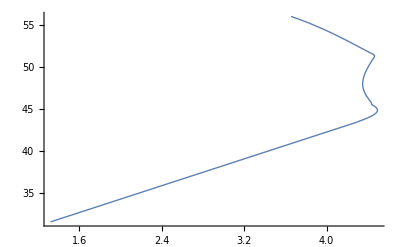

```mathematica
normalSN=ListPlot[Table[{logms,logQ},{logmdm,25,45.7,0.1}],Joined->True,PlotStyle->{Thick}]
```

```mathematica
endSN=Plot[q,{ms,1,3.64},PlotStyle->{Thick}];
```

```mathematica
q/.{ms->3.6}
```

56.1638